# θ_P Analytical_Resonance_Spectrum

```mathematica
Clear["Global`*"]
```

```mathematica
thetaP[gamma_,Omega_]:=((1-Omega^2)^2+4 gamma^2 Omega^2)^-0.5;
```

```mathematica
gamma = 0.25;
p1=Plot[thetaP[gamma,Omega],{Omega,0,2},PlotStyle->Blue];
```

```mathematica
gamma = 0.5;
p2=Plot[thetaP[gamma,Omega],{Omega,0,2},PlotStyle->Green];
```

```mathematica
gamma = 1;
p3=Plot[thetaP[gamma,Omega],{Omega,0,2},PlotStyle->Cyan];
```

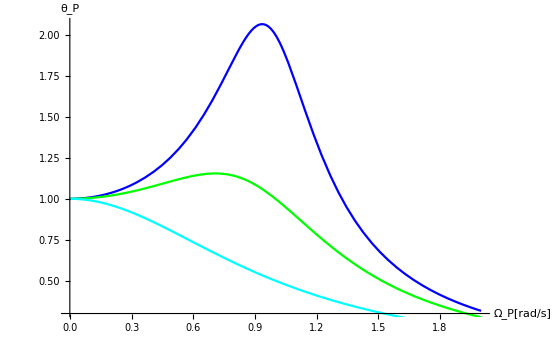

```mathematica
Show[p1,p2,p3,AxesLabel->{"Ω_P[rad/s]","θ_P"}]
```